## Full Excitation Pulse - Input Pulse Figure 3.1

```mathematica
PulseInput[g_,κ_,wa_,wb_]:=(g^2 κ/π)/(((wa-ⅈ κ)wa-g^2)((wb-ⅈ κ)wb-g^2));
Plot3D[Abs[PulseInput[1.,0.335046,wa,wb]],{wa,-2,2},{wb,-2,2},PlotRange->All]
```

-Graphics3D-

```mathematica
ImageCrop[Plot3D[Abs[PulseInput[1.,0.335046,wa,wb]],{wa,-2,2},{wb,-2,2},PlotRange->All,ImageSize->500,AxesLabel->{Style[Subscript[ω, a]/g,FontSize->24,Black],Style[Subscript[ω, b]/g,FontSize->24,Black],Style[Abs[Subscript[ξ, in]],FontSize->24,Black]},Boxed->True,TicksStyle->20,ColorFunction->Function[{x,y,z},Hue[z]]]]
```

-Graphics-

## Full Excitation Pulse - Output Pulse Figure 3.2

```mathematica
PulseOutput[g_,κ_,wa_,wb_]:=((κ+ⅈ wa)(κ+ⅈ wb))/((κ-ⅈ wa)(κ-ⅈ wb))((g^2 κ/π)/(((wa-ⅈ κ)wa-g^2)((wb-ⅈ κ)wb-g^2))(1-2 g^2 κ(1/((κ+ⅈ wa)(g^2-ⅈ wa(κ-ⅈ wa)))+1/((κ+ⅈ wb)(g^2-ⅈ wb(κ-ⅈ wb)))))-(2 g^6 κ^3/π)/((κ+ⅈ wa)(κ+ⅈ wb))*1/(g^2-(wa+wb) (wa+wb+ⅈ κ))((1/(g^2-wa (wa+ⅈ κ))+1/(g^2-wb (wb+ⅈ κ)))*2/((g^2+2 κ^2)(-g^2+(wa+wb)^2+3 ⅈ κ (wa+wb)-2 κ^2))-1/(g^2 (4 g^2-(wa+wb) (wa+wb-2 ⅈ κ)) (wa+wb-ⅈ κ) κ)*((((wa+wb) (wb-ⅈ κ) (wa+wb-2 ⅈ κ)+g^2 (3 wa+5 wb-2 ⅈ κ)) (-ⅈ wa+κ))/((g^2-wb (wb-ⅈ κ)) (g^2-wa (wa+ⅈ κ)))+(((wa+wb) (wa-ⅈ κ) (wa+wb-2 ⅈ κ)+g^2 (5 wa+3 wb-2 ⅈ κ)) (-ⅈ wb+κ))/((g^2-wa (wa-ⅈ κ)) (g^2-wb (wb+ⅈ κ)))))-(2κ-ⅈ(wa+wb))/((κ+ⅈ wa)(κ+ⅈ wb))*1/(2g^2+(κ-ⅈ(wa+wb))(2κ-ⅈ(wa+wb)))*(1/(g^2-ⅈ wa(κ-ⅈ wa))+1/(g^2-ⅈ wb(κ-ⅈ wb)))*(2 ⅈ g^6 κ^2 (2 (wa+wb-2 ⅈ κ) (wa+wb+2 ⅈ κ)^2 κ+ⅈ g^2 (3 (wa+wb)^2+10 ⅈ (wa+wb)κ+16 κ^2)))/(π (4 g^2-(wa+wb) (wa+wb-2 ⅈ κ)) (wa+wb-ⅈ κ) (wa+wb+2 ⅈ κ) (-g^2+wa^2+2 wa wb+wb^2+3 ⅈ wa κ+3 ⅈ wb κ-2 κ^2) (g^2+2 κ^2)));
Plot3D[Abs[PulseOutput[1.,0.335046,wa,wb]],{wa,-2,2},{wb,-2,2},AxesLabel->Abs[Subscript[ξ, out]],PlotRange->All]
```

-Graphics3D-

```mathematica
ImageCrop[Plot3D[Abs[PulseOutput[1.,0.335046,wa,wb]],{wa,-2,2},{wb,-2,2},PlotRange->All,ImageSize->500,AxesLabel->{Style[Subscript[ω, a]/g,FontSize->24,Black],Style[Subscript[ω, b]/g,FontSize->24,Black],Style[Abs[Subscript[ξ, out]],FontSize->24,Black]},Boxed->True,TicksStyle->20,ColorFunction->Function[{x,y,z},Hue[z]]]]
```

-Graphics-

## Phase plot for the output pulse with contour plot of the spectrum magnitude overlaid on it

```mathematica
cont=ContourPlot[Abs[PulseInput[1.,0.335046,wa,wb]],{wa,-2.1,2.1},{wb,-2.1,2.1},PlotRange->All,ContourShading->None];
```

```mathematica
col2[v_]:=ColorData["BalancedHue"][Rescale[v,{0,2π}]];
```

### Figure 3.3

```mathematica
outpulse=DensityPlot[Mod[Arg[PulseOutput[1.,0.335046,wa,wb]]/π,2.2],{wa,-2.1,2.1},{wb,-2.1,2.1},ColorFunction->ColorData["BalancedHue"],FrameLabel->{Style["ω_a/g",FontFamily->"Caladea",Black,Italic,24],Style["ω_b/g",FontFamily->"Caladea",Black,Italic,24]},Frame->True,FrameTicksStyle->Directive[Black,15],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Style["Φ/π",Black,24]],{After,Top}],ColorFunction->Hue];
```

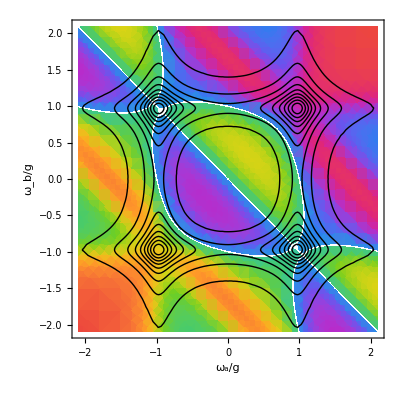

```mathematica
outpulse2=Show[outpulse,cont]
```

### Figure 3.4

```mathematica
inpulse=DensityPlot[Mod[Arg[-PulseInput[1.,0.335046,wa,wb]]/π,2],{wa,-2.1,2.1},{wb,-2.1,2.1},ColorFunction->ColorData["BalancedHue"],FrameLabel->{Style["ω_a/g",FontFamily->"Caladea",Black,Italic,24],Style["ω_b/g",FontFamily->"Caladea",Black,Italic,24]},Frame->True,FrameTicksStyle->Directive[Black,15],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Style["Φ/π",Black,24]],{After,Top}],ColorFunction->Hue];
```

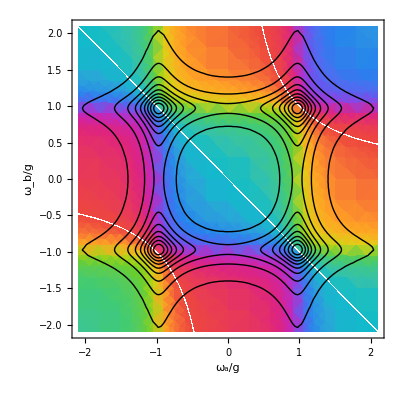

```mathematica
inpulse2=Show[inpulse,cont]
```

### Figure 3.5

```mathematica
trinpulse=DensityPlot[Mod[Arg[Conjugate[-PulseInput[1.,0.335046,wa,wb]]]/π,2],{wa,-2.1,2.1},{wb,-2.1,2.1},ColorFunction->ColorData["BalancedHue"],FrameLabel->{Style["ω_a/g",FontFamily->"Caladea",Black,Italic,24],Style["ω_b/g",FontFamily->"Caladea",Black,Italic,24]},Frame->True,FrameTicksStyle->Directive[Black,15],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Style["Φ/π",Black,24]],{After,Top}],ColorFunction->Hue];
```

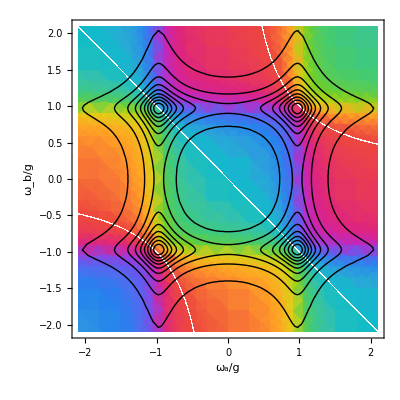

```mathematica
trinpulse2=Show[trinpulse,cont]
```